```mathematica
PDF[CauchyDistribution[0,a],x]
```

1/(a π (1+x^2/a^2))

```mathematica
(*Half Cauchy density, alpha is scale parameter. x is R.V. IE, x ~ Half-Cauchy(alpha) with x ≥ 0)
2*PDF[CauchyDistribution[0,α],x] *)
f[x_,α_]:=2/(π (1+x^2/α^2) α)
```

```mathematica
(*Half Cauchy CDF*) 
∫_0^xp f[x,a]ⅆx
```

ConditionalExpression[(2 ArcTan[xp/a])/π,Re[a/xp]≠0||Im[a/xp]>1||Im[a/xp]<-1]

```mathematica
(*Quantile function??*)
Solve[p==(2 ArcTan[xp/a])/π,xp]
```

{{xp→ConditionalExpression[a Tan[(p π)/2],(-π≤π Re[p]<π&&π Im[p]<0)||-π<π Re[p]<π||(-π<π Re[p]≤π&&π Im[p]>0)]}}

```mathematica
qf[p_,a_]:=a Tan[(p π)/2];
```

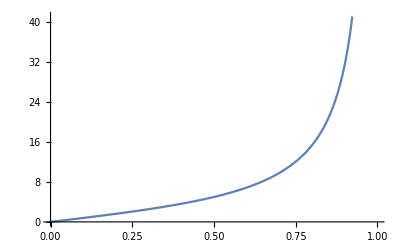

```mathematica
Plot[qf[p,5],{p,0,1}]
```

```mathematica
(*Now just examine the Cauchy distribution:*)
CDF[CauchyDistribution[0,a],x]
```

1/2+ArcTan[x/a]/π

```mathematica
Solve[p==1/2+ArcTan[x/a]/π,x]
```

{{x→ConditionalExpression[a Tan[1/2 (-1+2 p) π],(-π≤-π+2 π Re[p]<π&&π Im[p]<0)||-π<-π+2 π Re[p]<π||(-π<-π+2 π Re[p]≤π&&π Im[p]>0)]}}

```mathematica
(*Quantile function for the Cauchy dist:*)
qfcd[p_,a_]:=a Tan[1/2 (-1+2 p) π];
```

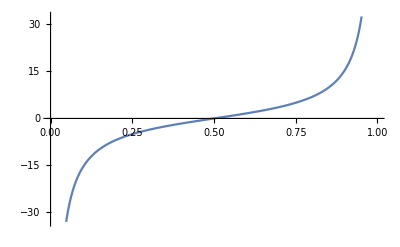

```mathematica
Plot[qfcd[p,5],{p,0,1}]
```